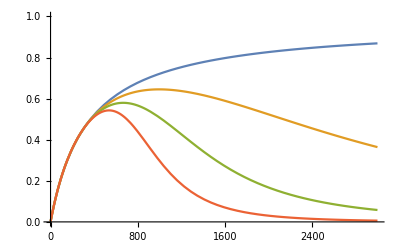

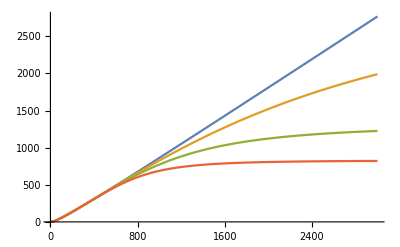

NIntegrate::inumr: The integrand (31 x)/(1000 (1+(63 x)/2000+3^(1-n) 4^(-1-n) 5^(-1-2 n) x^n)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3000}}.

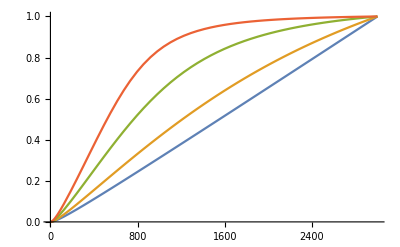

```mathematica
Clear["Global`*"]
(* weak promoter, assume P is very very small, group P and ω into one parameter ω'*)
pBound3[d_,kd1_,kd2_,ω_,n_] = ((d/kd1)*ω) /(((d/kd1)*ω)+ (d/kd1)+(d^n/(kd1*kd2^(n-1))+1));
Manipulate[Plot[pBound3[d,kd1,kd2,ω,n], {d, 1,3000}, PlotRange->{{0 ,3000}, {0, 1}}], {kd1, 1, 60000},{kd2, .01, 1000}, {n, 1, 7},{ω, 1, 1100}];

(* show the integral of the previous function*)
Manipulate[Plot[{NIntegrate[pBound3[x,kd1,kd2,ω,n],{x,0,d}]},{d,1,3000}],{kd1,1,60000},{kd2,.01,100000},{n,1,7},{ω,1,1100}]



(* plot for different values of n on the same graph, without mannipulate*)
Plot[{pBound3[d,22000,300,62,1],pBound3[d,22000,300,62,3],pBound3[d,22000,300,62,4],pBound3[d,22000,300,62,5]}, {d, 1,3000}, PlotRange->{{0 ,3000}, {0, 1}}]


(* plot the integral for different values of n on the same graph, without mannipulate*)
Plot[{NIntegrate[pBound3[x,2000,300,62,1],{x,0,d}],NIntegrate[pBound3[x,2000,300,62,3],{x,0,d}],NIntegrate[pBound3[x,2000,300,62,4],{x,0,d}],NIntegrate[pBound3[x,2000,300,62,5],{x,0,d}]},{d,1,3000}]

(*NormNIntegrate[x_,kd1_,kd2_,ω_,n_]=NIntegrate[pBound3[x_,kd1_,kd2_,ω_,n_],{x,0,d}]*)

(* plot the normalized integral for different values of n on the same graph, without mannipulate*)
NormFun[x_,n_] = NIntegrate[pBound3[x,2000,300,62,n],{x,0,3000}]; (*normalization function*)

Plot[{NIntegrate[pBound3[x,2000,300,62,1],{x,0,d}]/NormFun[x,1],NIntegrate[pBound3[x,2000,300,62,3],{x,0,d}]/NormFun[x,3],NIntegrate[pBound3[x,2000,300,62,4],{x,0,d}]/NormFun[x,4],NIntegrate[pBound3[x,2000,300,62,5],{x,0,d}]/NormFun[x,5]},{d,1,3000}]
```

```mathematica
(d ω)/(kd1 (1+d/kd1+(d^n kd2^(1-n))/kd1+(d ω)/kd1))
```

```mathematica
(*pBound4[x_,kd1_,kd2_,ω_] = ((x/kd1)*ω) /(((x/kd1)*ω)+ (x/kd1)+(x^3/(kd1*kd2^2)+1));
pBoundInt[x_,kd1_,kd2_,ω_]  = Integrate[pBound4[x,kd1,kd2,ω],x]
(*N[Normal[%]]*)
Manipulate[Plot[N[pBoundInt[x,kd1,kd2,ω]], {x, 1,3000}, PlotRange->{{0 ,3000}, {0, 10}}], {kd1, 1, 30000},{kd2, .01, 100000},{ω, 1, 1100}]
```

```mathematica
pBound3[x,2000,300,62,3]
```